```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
files1=FileNames["TYPES_N100_g500_runs1_pswitch0.0000_pintro0.0*_Tmut*_types2_*.txt"];
Data1=Table[Import[files1[[f]],"Table"],{f,1,Length[files1]}];

files2=FileNames["TYPES_N500_g500_runs1_pswitch0.0000_pintro0.0*_Tmut*_types2_*.txt"];
Data2=Table[Import[files2[[f]],"Table"],{f,1,Length[files2]}];

files3=FileNames["TYPES_N1000_g500_runs1_pswitch0.0000_pintro0.0*_Tmut*_types2_*.txt"];
Data3=Table[Import[files3[[f]],"Table"],{f,1,Length[files3]}];

files4=FileNames["TYPES_N5000_g500_runs1_pswitch0.0000_pintro0.0*_Tmut*_types2_*.txt"];
Data4=Table[Import[files4[[f]],"Table"],{f,1,Length[files4]}];

(*files5=FileNames["TYPES_N1000_g800_runs10000_pswitch0.0000_pintro0.000_Tmut795_types2_*var0.00_mean0.000_pSize0.000.txt.txt"];
Data5=Table[Import[files5[[f]],"Table"],{f,1,Length[files5]}];*)
```

```mathematica
ratios1 = Table[Table[Min[Data1[[j]][[i]]]/Max[Data1[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data1][[1]]}]*1.0;
ratios2 = Table[Table[Min[Data2[[j]][[i]]]/Max[Data2[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data2][[1]]}]*1.0;
ratios3 = Table[Table[Min[Data3[[j]][[i]]]/Max[Data3[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data3][[1]]}]*1.0;
ratios4 =Table[Table[Min[Data4[[j]][[i]]]/Max[Data4[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data4][[1]]}]*1.0;
(*ratios5 = Table[Table[Min[Data5[[j]][[i]]]/Max[Data5[[j]][[i]]], {i,2, 800}],{j,1,Dimensions[Data5][[1]]}]*1.0;*)

meanRatios1 = Mean[ratios1];
meanRatios2 = Mean[ratios2];
meanRatios3 = Mean[ratios3];
meanRatios4 = Mean[ratios4];
meanRatios5 = Mean[ratios5];
```

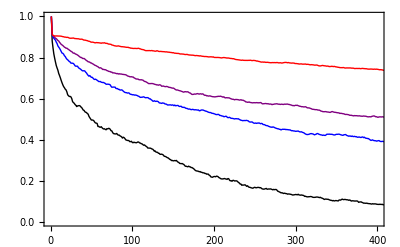

```mathematica
Show[ListLinePlot[{meanRatios1, meanRatios2, meanRatios3, meanRatios4}, PlotRange->{{0,400},{0,1}}, PlotStyle->{{Black,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick}}], Frame->True,FrameTicksStyle->Directive[16, Black,FontFamily-> "Times"]]
```

```mathematica
filesExt1=FileNames["p_N1000_g800_runs10000_pswitch*_pintro0.010_Tmut795_types10_*_var0.00_mean0.000_pSize0.000.txt.txt"];
DataExt1=Table[Import[filesExt1[[f]],"Table"],{f,1,Length[filesExt1]}];

filesExt2=FileNames["p_N1000_g800_runs10000_pswitch*_pintro0.050_Tmut795_types10_*_var0.00_mean0.000_pSize0.000.txt.txt"];
DataExt2=Table[Import[filesExt2[[f]],"Table"],{f,1,Length[filesExt2]}];

filesExt3=FileNames["p_N1000_g800_runs10000_pswitch*_pintro0.100_Tmut795_types10_*_var0.00_mean0.000_pSize0.000.txt.txt"];
DataExt3=Table[Import[filesExt3[[f]],"Table"],{f,1,Length[filesExt3]}];

filesExt4=FileNames["p_N1000_g800_runs10000_pswitch*_pintro0.250_Tmut795_types10_*var0.00_mean0.000_pSize0.000.txt.txt"];
DataExt4=Table[Import[filesExt4[[f]],"Table"],{f,1,Length[filesExt4]}];
```

```mathematica
Mean[Flatten[Table[Position[Flatten[DataExt01[[i]]],_?(#==0&)][[1]], {i,1,Dimensions[DataExt01][[1]]}]]]*1.0
Flatten[Table[Position[Flatten[DataExt01[[i]]],_?(#==0&)][[1]], {i,1,Dimensions[DataExt01][[1]]}]]

(*Mean[Flatten[Table[Position[Flatten[DataExt005[[i]]],_?(#==0&)][[1]], {i,1,Dimensions[DataExt005][[1]]}]]]*1.0
Flatten[Table[Position[Flatten[DataExt005[[i]]],_?(#==0&)][[1]], {i,1,Dimensions[DataExt005][[1]]}]]*)
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

1. Mean[Table[Position[Flatten[DataExt01⟦i⟧],_?(#1==0&)]⟦1⟧,{i,1,{}⟦1⟧}]]

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Table[Position[Flatten[DataExt01⟦i⟧],_?(#1==0&)]⟦1⟧,{i,1,{}⟦1⟧}]

```mathematica
ext1 = Table[sum=0;
For[i=1, i<Length[filesExt1], i++, If[Flatten[DataExt1[[i]]][[j]]==0, sum++]];sum, {j,1,799}]/Length[filesExt1]*1.0;

ext2 = Table[sum=0;
For[i=1, i<Length[filesExt2], i++, If[Flatten[DataExt2[[i]]][[j]]==0, sum++]];sum, {j,1,799}]/Length[filesExt2]*1.0;

ext3 = Table[sum=0;
For[i=1, i<Length[filesExt3], i++, If[Flatten[DataExt3[[i]]][[j]]==0, sum++]];sum, {j,1,799}]/Length[filesExt3]*1.0;

ext4 = Table[sum=0;
For[i=1, i<Length[filesExt4], i++, If[Flatten[DataExt4[[i]]][[j]]==0, sum++]];sum, {j,1,799}]/Length[filesExt4]*1.0;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
Show[ListLinePlot[{ext1, ext2, ext3, ext4}, PlotStyle->{Thick, RGBColor}, PlotRange->{{0,500},{0,1}}], Frame->True,FrameTicksStyle->Directive[16,Black]]
```

-Graphics-